Momentum:

-Graphics-

Position:

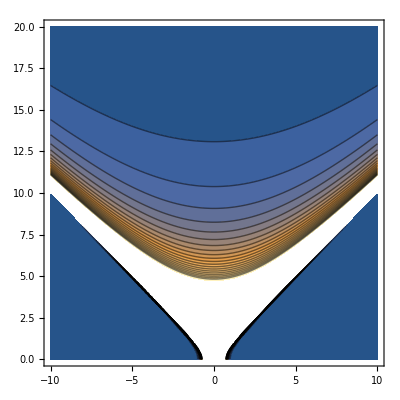

```mathematica
m=4;
"Momentum:"
ContourPlot[Abs[1/(e^2-p^2-m^2)]^2,{p,-10,10},{e,0,20},PlotPoints->60,Contours->20]
τ2=t^2-x^2;
"Position:"
ContourPlot[Abs[Piecewise[{{-DiracDelta[τ2]/(4π)+m*HankelH2[1,m*Sqrt[τ2]]/(8π*Sqrt[τ2]),τ2≥0},{-ⅈ*m/(4π^2*Sqrt[-τ2])*BesselK[1,m*Sqrt[-τ2]],τ2<0}}]]^2,{x,-10,10},{t,0,20},PlotPoints->60,Contours->20]
```